## Dyskretyzacja filtru

```mathematica
data=Table[ Sin[x]+RandomReal[.5],{x,0,2 Pi, 0.05}];
Length@data;
fir={1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
```

```mathematica
ker=FrequencySamplingFilterKernel[fir];
firLen=Length@fir;
signalPerf=ListConvolve[ker,data,firLen];
spectrumPerf=Abs@Fourier[signalPerf, FourierParameters->{-1, 1}];
DiscretizeData[x_,bits_]:=Module[{max},max=Max[x]; If[#>0,1,-1]Round[(Abs[#]/max)(Power[2,bits-1]-1)] max/(Power[2,bits-1]-1) &/@x];
RoundData[x_,bits_]:=Round[x,2^-bits];
SpectrumError[spectrum_]:=Sqrt[Total[Abs[(spectrum-spectrumPerf)]^2]/((Total[Abs[spectrum]^2] ) )];
```

```mathematica
Manipulate[Module[{dataD,kerD,max,spectrumK,spectrumD,spectrumKD,signalK,signalD,signalKD,errK,errD,errKD},
dataD=df[data,n];
kerD=ff[ker,m];

signalK=ListConvolve[kerD,data,firLen];
signalD=ListConvolve[ker,dataD,firLen];
signalKD=ListConvolve[kerD,dataD,firLen];

spectrumK=Abs@Fourier[signalK, FourierParameters->{-1, 1}];
spectrumD=Abs@Fourier[signalD, FourierParameters->{-1, 1}];
spectrumKD=Abs@Fourier[signalKD, FourierParameters->{-1, 1}];

errK=Quiet@SpectrumError[spectrumK];
errD=Quiet@SpectrumError[spectrumD];
errKD=Quiet@SpectrumError[spectrumKD];

Grid[{{Plot[Abs[ListFourierSequenceTransform[ker,x]],{x,0,π},PlotRange->All,PlotLabel->"Filtr",ImageSize->Medium],ListLinePlot[{signalPerf},ImageSize->Medium,PlotRange->Full, PlotLabel->"Bez przybliżeń "],ListLinePlot[{signalD},ImageSize->Medium,PlotRange->Full,PlotLabel->"Przybliżenie sygnału, błąd="<>ToString[errD]]},
{ListLinePlot[{data},ImageSize->Medium,PlotRange->Full,PlotLabel->"sygnał"],ListLinePlot[{signalK},ImageSize->Medium,PlotRange->Full, PlotLabel->"Przybliżenie filtru, błąd=" <>ToString[errK]],
ListLinePlot[{signalKD},ImageSize->Medium,PlotRange->Full,PlotLabel->"Przybliżenie sygnału i filtru, błąd="<>ToString[errKD]]}}]]
,{{n,2,"Przybliżenie sygnału"},0,32,1,Appearance->"Open"},{{m,2,"Przybliżenie filtru "},0,32,1,Appearance->"Open"},{{df,DiscretizeData,"Metoda przybliżenia sygnału"},{DiscretizeData->"Dyskretyzacja na n-bitach",RoundData->"Round[x,2^-n]"}},{{ff,DiscretizeData,"Metoda przybliżenia filtru"},{DiscretizeData->"Dyskretyzacja na n-bitach",RoundData->"Round[x,2^-n]"}}]
```

```mathematica
wyniki=Table[{m,n,Quiet@Log@SpectrumError[Abs@Fourier[ListConvolve[DiscretizeData[ker,m],DiscretizeData[data,n],firLen], FourierParameters->{-1, 1}]]},{m,2,32,2},{n,2,32,2}];
wyniki=Flatten[wyniki,1];
```

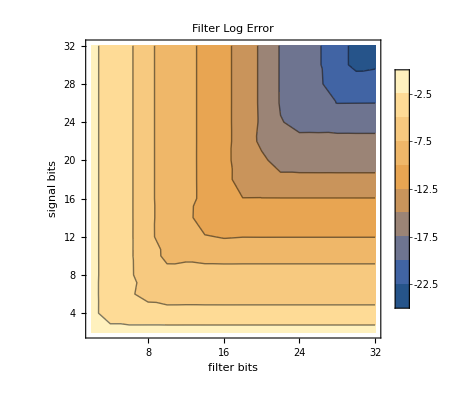

```mathematica
ListContourPlot[wyniki,PlotLegends->Automatic,LabelStyle->Directive[Bold],FrameLabel->{"filter bits","signal bits"},PlotLabel->"Filter Log Error"]
```